ЛАБОРАТОРНАЯ РАБОТА № 4

Номер 1

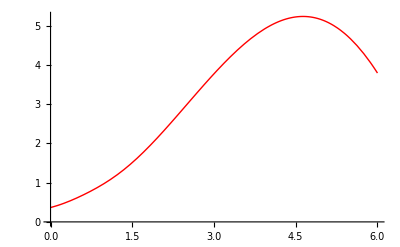

```mathematica
a =0;
b= 6;
n1 = 6;
n2 = 10;
h1 = (b-a)/n1;
h2 = (b-a)/n2;
f[x_]=(x^6+4 x^2+1)^(1/5)*Sin[(2*x/√31+1/7*√(x+5)+1/18)];
graph = Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
tabl1 = N[Table[{a+i*h1,f[a+i*h1]},{i,0,n1}]]
tabl2 = N[Table[{a+i*h2,f[a+i*h2]},{i,0,n2}]]
{TableForm[tabl1]}
{TableForm[tabl2]}
```

{{0.,0.366267},{1.,0.990682},{2.,2.20005},{3.,3.77226},{4.,4.97336},{5.,5.13549},{6.,3.79068}}

{{0.,0.366267},{0.6,0.686507},{1.2,1.17656},{1.8,1.90721},{2.4,2.82599},{3.,3.77226},{3.6,4.58328},{4.2,5.10759},{4.8,5.21258},{5.4,4.79492},{6.,3.79068}}

{0. | 0.366267
1. | 0.990682
2. | 2.20005
3. | 3.77226
4. | 4.97336
5. | 5.13549
6. | 3.79068}

{0. | 0.366267
0.6 | 0.686507
1.2 | 1.17656
1.8 | 1.90721
2.4 | 2.82599
3. | 3.77226
3.6 | 4.58328
4.2 | 5.10759
4.8 | 5.21258
5.4 | 4.79492
6. | 3.79068}

Номер 1 (а): 
Введем вспомогательные члены

```mathematica
P1[x_]=∏_(i=0)^n1 (x-tabl1[[i+1,1]])
P2[x_]=∏_(i=0)^n2 (x-tabl2[[i+1,1]])
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)

Составим интерполяционные многочлены Лагранджа

```mathematica
L1[x_]=Sum[tabl1[[i+1,2]] P1[x]/((x-tabl1[[i+1,1]]) P1'[tabl1[[i+1,1]]]),{i,0,n1}]//Simplify
L2[x_]=Sum[tabl2[[i+1,2]] P2[x]/((x-tabl2[[i+1,1]]) P2'[tabl2[[i+1,1]]]),{i,0,n2}]//Simplify
```

0.366267+0.575475 x-0.240887 x^2+0.398293 x^3-0.121917 x^4+0.0140682 x^5-0.000616806 x^6

0.366267+0.228573 x+1.10121 x^2-1.74428 x^3+1.73002 x^4-0.948462 x^5+0.314306 x^6-0.0654441 x^7+0.00839404 x^8-0.000606875 x^9+0.0000189416 x^10

Изобразим, что получилось

График точек из таблицы значений 1:

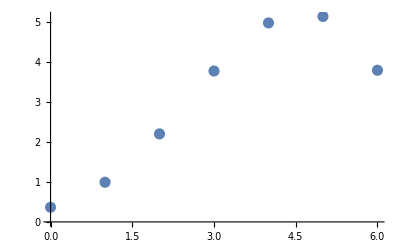

```mathematica
graph1D=ListPlot[tabl1,PlotStyle->{Darker,PointSize[0.02]}]
```

График интерполяции 1:

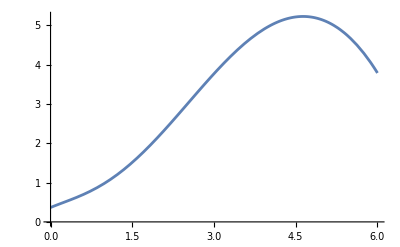

```mathematica
graphL1=Plot[L1[x],{x,a,b}]
```

График совмещенный:

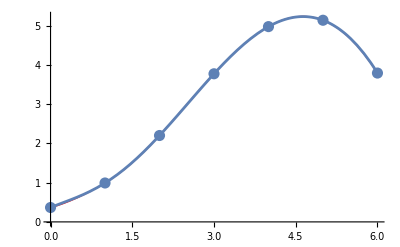

```mathematica
Show[graph,graph1D,graphL1]
```

График точек из таблицы значений 2:

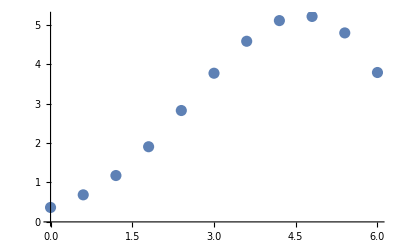

```mathematica
graph2D=ListPlot[tabl2,PlotStyle->{Darker,PointSize[0.02]}]
```

График интерполяции 2:

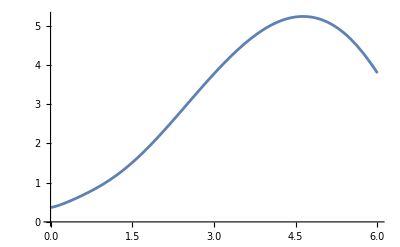

```mathematica
graphL2=Plot[L2[x],{x,a,b}]
```

График совмещенный:

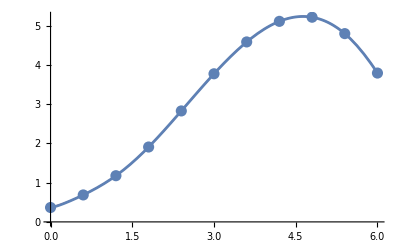

```mathematica
Show[graph,graph2D,graphL2]
```

Номер 1 (б):
Составим таблицу конечных разностей (пустоты заполним)

Для n = 6:

```mathematica
Array[dif1,{n1+1,n1+1},{0,0}];
For[k=1,k≤n1,k++,
For[i=n1,i≥n1-k,i--,dif1[i,k]="    *    "]];
For[i=0,i≤n1,i++,dif1[i,0]=tabl1[[i+1,2]]];
For[k=1,k≤n1,k++,
For[i=0,i≤n1-k,i++,
dif1[i,k]=dif1[i+1,k-1]-dif1[i,k-1]]];
diftabl1=Array[dif1,{n1+1,n1+1},{0,0}];
PaddedForm[TableForm[diftabl1],{n1,n1-1}]
```

0.36627 |  0.62442 |  0.58495 | -0.22210 | -0.51185 |  0.57794 | -0.44410
 0.99068 |  1.20936 |  0.36285 | -0.73395 |  0.06608 |  0.13384 |     *    
 2.20005 |  1.57221 | -0.37111 | -0.66787 |  0.19992 |     *     |     *    
 3.77226 |  1.20110 | -1.03898 | -0.46795 |     *     |     *     |     *    
 4.97336 |  0.16213 | -1.50693 |     *     |     *     |     *     |     *    
 5.13549 | -1.34481 |     *     |     *     |     *     |     *     |     *    
 3.79068 |     *     |     *     |     *     |     *     |     *     |     *

Для n = 10:

```mathematica
Array[dif2,{n2+1,n2+1},{0,0}];
For[k=1,k≤n2,k++,
For[i=n2,i≥n2-k,i--,dif2[i,k]="    *    "]];
For[i=0,i≤n2,i++,dif2[i,0]=tabl2[[i+1,2]]];
For[k=1,k≤n2,k++,
For[i=0,i≤n2-k,i++,
dif2[i,k]=dif2[i+1,k-1]-dif2[i,k-1]]];
diftabl2=Array[dif2,{n2+1,n2+1},{0,0}];
PaddedForm[TableForm[diftabl2],{n2,n2-1}]
```

0.366266795 |  0.320239735 |  0.169814143 |  0.070781721 | -0.123247130 |  0.015068924 |  0.091020945 | -0.183755945 |  0.270722381 | -0.349070726 |  0.415615403
 0.686506530 |  0.490053877 |  0.240595863 | -0.052465409 | -0.108178205 |  0.106089870 | -0.092735000 |  0.086966436 | -0.078348345 |  0.066544677 |     *    
 1.176560408 |  0.730649741 |  0.188130454 | -0.160643614 | -0.002088336 |  0.013354870 | -0.005768564 |  0.008618091 | -0.011803668 |     *     |     *    
 1.907210148 |  0.918780195 |  0.027486840 | -0.162731950 |  0.011266534 |  0.007586305 |  0.002849526 | -0.003185577 |     *     |     *     |     *    
 2.825990343 |  0.946267035 | -0.135245111 | -0.151465417 |  0.018852839 |  0.010435832 | -0.000336051 |     *     |     *     |     *     |     *    
 3.772257378 |  0.811021924 | -0.286710527 | -0.132612578 |  0.029288670 |  0.010099780 |     *     |     *     |     *     |     *     |     *    
 4.583279301 |  0.524311396 | -0.419323105 | -0.103323908 |  0.039388451 |     *     |     *     |     *     |     *     |     *     |     *    
 5.107590698 |  0.104988291 | -0.522647013 | -0.063935457 |     *     |     *     |     *     |     *     |     *     |     *     |     *    
 5.212578989 | -0.417658722 | -0.586582470 |     *     |     *     |     *     |     *     |     *     |     *     |     *     |     *    
 4.794920266 | -1.004241192 |     *     |     *     |     *     |     *     |     *     |     *     |     *     |     *     |     *    
 3.790679074 |     *     |     *     |     *     |     *     |     *     |     *     |     *     |     *     |     *     |     *

Номер 1 (в):
Составим интерполяционные многочлены Ньютона (второй)

```mathematica
q1=(x-b)/h1;P1[x_]=dif1[n1,0];Pq1[q_]=1;
For[k=1,k≤n1,k++,Pq1[q_]=Pq1[q1]*(q1+k-1);P1[x_]=P1[x]+Pq1[q1]/(k!) dif1[n1-k,k]];
P1[x]//Simplify

q2=(x-b)/h2;P2[x_]=dif2[n2,0];Pq2[q_]=1;
For[k=1,k≤n2,k++,Pq2[q_]=Pq2[q2]*(q2+k-1);P2[x_]=P2[x]+Pq2[q2]/(k!) dif2[n2-k,k]];
P2[x]//Simplify
```

0.366267+0.575475 x-0.240887 x^2+0.398293 x^3-0.121917 x^4+0.0140682 x^5-0.000616806 x^6

0.366267+0.228573 x+1.10121 x^2-1.74428 x^3+1.73002 x^4-0.948462 x^5+0.314306 x^6-0.0654441 x^7+0.00839404 x^8-0.000606875 x^9+0.0000189416 x^10

Изобразим их

```mathematica
graph1P=Plot[P1[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graph,graph1D,graph1P]
```

-Graphics-

```mathematica
graph2P=Plot[P2[x],{x,a,b}]
```

-Graphics-

```mathematica
Show[graph,graph2D,graph2P]
```

-Graphics-

Номер1 (г):
Составим интерполяционные многочлены Ньютона(2) с помощью встроенных пакетов

```mathematica
Np1[x_]=InterpolatingPolynomial[tabl1,x]//Simplify
Np2[x_]=InterpolatingPolynomial[tabl2,x]//Simplify
```

0.366267+0.575475 x-0.240887 x^2+0.398293 x^3-0.121917 x^4+0.0140682 x^5-0.000616806 x^6

0.366267+0.228573 x+1.10121 x^2-1.74428 x^3+1.73002 x^4-0.948462 x^5+0.314306 x^6-0.0654441 x^7+0.00839404 x^8-0.000606875 x^9+0.0000189416 x^10

```mathematica
graph1Np=Plot[Np1[x],{x,a,b}]
Show[graph,graph1D,graph1Np]
```

-Graphics-

-Graphics-

```mathematica
graph2Np=Plot[Np2[x],{x,a,b}]
Show[graph,graph2D,graph2Np]
```

-Graphics-

-Graphics-

Все из полученных интерполяционных многочленов в узлах интерполяции совпадают с изначальной функцией, следовательно, все из них могут считаться мало отличающимися от f(x).

Номер 1 (д):

```mathematica
x0=2.4316;
Print["f[x0]=",f[x0]]
Print["L1[x0]=",L1[x0],", L2[x0]=",L2[x0]]


Print["P1[x0]=",P1[x0],", P2[x0]=",P2[x0]]

Print["Np1[x0]=",Np1[x0],", Np2[x0]=",Np2[x0]]
```

f[x0]=2.8766

L1[x0]=2.87389, L2[x0]=2.87663

P1[x0]=2.87389, P2[x0]=2.87663

Np1[x0]=2.87389, Np2[x0]=2.87663

Исходя из полученных графиков и значений в точке x0, отметим, что интерполяционные многочлены, полученные различными способами, либо совпадают полностью, либо имеют незначительные отличия, а использование большего числа узлов увеличивает точность аппроксимации.

Номер 1 (е):
Построим график погрешности интерполирования многочленом Ньютона

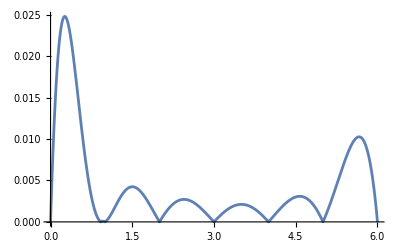

{0.0247999,{x→0.261447}}

```mathematica
R1[x_]=Abs[f[x]-Np1[x]];
graphErr1=Plot[R1[x],{x,a,b},PlotRange->Full]
maxErr1=FindMaximum[R1[x],{x,a,b}]
```

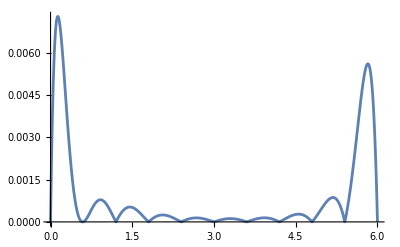

{0.0072881,{x→0.133414}}

```mathematica
R2[x_]=Abs[f[x]-Np2[x]];
graphErr2=Plot[R2[x],{x,a,b},PlotRange->Full]
maxErr2=FindMaximum[R2[x],{x,a,b}]
```

Номер 1 (ж) :
Исходя из полученных графиков погрешностей, можно сделать вывод, что с увеличением степени интерполяционного многочлена n погрешность интерполирования уменьшается (значение maxErr1 значительно больше значения maxErr2).